```mathematica
Map[ColorShape,Select[FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,4}]]],SymbolLevel[#]==4&]]
```

{1♁24♁3♁56,1♁24♁35♁6,14♁2♁3♁56,14♁2♁35♁6,14♁25♁3♁6,13♁2♁4♁56,13♁25♁4♁6,13♁24♁5♁6}

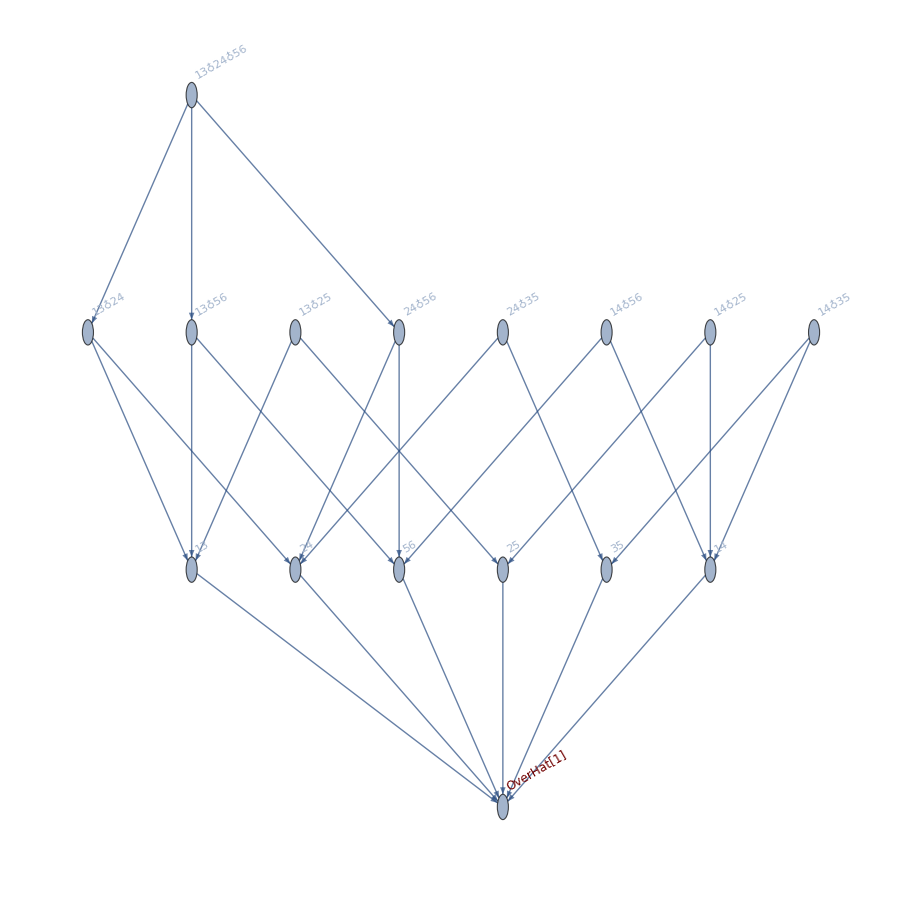

```mathematica
FormulaGraphReverse[FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,4}]]]]
```

```mathematica
Map[ColorShape,Select[FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,1}]]],SymbolLevel[#]==4&]]
```

{1♁2♁356♁4,1♁2♁35♁46,1♁26♁35♁4,1♁256♁3♁4,1♁25♁3♁46,1♁25♁36♁4,1♁246♁3♁5,1♁24♁3♁56,1♁24♁36♁5,1♁24♁35♁6,14♁2♁3♁56,14♁2♁36♁5,14♁2♁35♁6,14♁26♁3♁5,14♁25♁3♁6,13♁2♁4♁56,13♁2♁46♁5,13♁26♁4♁5,13♁25♁4♁6,13♁24♁5♁6}

```mathematica
TableForm[
Sort[
Table[
With[{formula=FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,sets}]]]},
{SetsToLabel[{sets}],Length[Select[formula,SymbolLevel[#]==4&]],Multicolumn[Select[Sort[Tally[Map[WhichQuadrilateralPattern[SymbolToSets[#]]&,Select[formula,SymbolLevel[#]==4&]]]],#[[1]]≠-1&]],Multicolumn[Select[Sort[Tally[Map[WhichTrianglePattern[SymbolToSets[#]]&,Select[formula,SymbolLevel[#]==4&]]]],#[[1]]≠-1&]],Framed[Multicolumn[Map[ColorShape,Select[formula,SymbolLevel[#]==4&]]]]}
]
,{sets,Subsets[Range[5]]}],#1[[2]]<#2[[2]]&
]
,
TableDepth->2,
TableHeadings->{None, {"connected to 6","count4", "count4 quad", "count4 tria", "solutions 4"}}]
```

connected to 6 | count4 | count4 quad | count4 tria | solutions 4
12345 | 5 |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
14♁2♁35♁6 | 13♁25♁4♁6 | 
 | 5 | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  |  | 1♁2♁35♁4 | 1♁24♁3♁5 | 13♁2♁4♁5
1♁25♁3♁4 | 14♁2♁3♁5 | 
2345 | 8 | {3,1} | {5,1}
{4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁24♁35♁6 | 16♁24♁3♁5 | 13♁25♁4♁6
16♁2♁35♁4 | 14♁2♁35♁6 | 13♁24♁5♁6
16♁25♁3♁4 | 14♁25♁3♁6 | 
1345 | 8 | {1,1} | {5,1}
{2,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
14♁2♁35♁6 | 13♁26♁4♁5 | 
1245 | 8 | {2,1} | {4,1}
{3,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁25♁36♁4 | 14♁2♁36♁5 | 13♁25♁4♁6
1♁24♁36♁5 | 14♁2♁35♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 14♁25♁3♁6 | 
1235 | 8 | {1,1} | {5,1}
{4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 13♁2♁46♁5 | 
1234 | 8 | {1,1} | {3,1}
{2,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁24♁3♁56 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
14♁2♁3♁56 | 13♁2♁4♁56 | 
345 | 11 | {1,1} | {3,1} | {5,2}
{2,1} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 16♁25♁3♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁24♁35♁6 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
16♁2♁35♁4 | 14♁2♁35♁6 | 13♁26♁4♁5 | 
234 | 11 | {1,1} | {3,2} | {5,1}
{2,1} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁24♁3♁56 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁35♁6 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
16♁2♁35♁4 | 14♁2♁3♁56 | 13♁2♁4♁56 | 
145 | 11 | {1,1} | {3,1} | {5,1}
{2,2} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 1♁24♁35♁6 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁25♁36♁4 | 14♁2♁36♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁36♁5 | 14♁2♁35♁6 | 13♁26♁4♁5 | 
125 | 11 | {1,1} | {3,1} | {5,1}
{2,1} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁24♁36♁5 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁25♁36♁4 | 14♁2♁36♁5 | 13♁2♁46♁5 | 
123 | 11 | {1,2} | {3,1} | {5,1}
{2,1} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 14♁2♁3♁56 | 13♁2♁4♁56 | 13♁24♁5♁6
1♁24♁3♁56 | 14♁2♁35♁6 | 13♁2♁46♁5 | 
245 | 12 | {1,1} | {3,2} | {5,1}
{2,1} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁36♁5 | 136♁2♁4♁5
1♁24♁36♁5 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁35♁6 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
235 | 12 | {1,1} | {3,1} | {5,2}
{2,1} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 16♁2♁35♁4 | 146♁2♁3♁5 | 13♁2♁46♁5
1♁25♁3♁46 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁35♁6 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
135 | 12 | {1,2} | {3,1} | {5,2}
{2,1} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁26♁35♁4 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 14♁2♁35♁6 | 13♁2♁46♁5 | 13♁24♁5♁6
134 | 12 | {1,2} | {3,1} | {5,1}
{2,2} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 1♁24♁35♁6 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁256♁3♁4 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁24♁3♁56 | 14♁2♁35♁6 | 13♁2♁4♁56 | 13♁24♁5♁6
124 | 12 | {1,1} | {3,2} | {5,1}
{2,2} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁36♁5 | 14♁2♁36♁5 | 13♁2♁4♁56
1♁25♁36♁4 | 1♁24♁35♁6 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁3♁56 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁24♁5♁6
45 | 15 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 16♁2♁35♁4 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁25♁36♁4 | 16♁25♁3♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁24♁36♁5 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 14♁2♁36♁5 | 136♁2♁4♁5 | 
34 | 15 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 16♁2♁35♁4 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁256♁3♁4 | 16♁25♁3♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁24♁3♁56 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 14♁2♁3♁56 | 13♁2♁4♁56 | 
23 | 15 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 16♁2♁35♁4 | 14♁2♁3♁56 | 13♁2♁46♁5
1♁25♁3♁46 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁3♁56 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 146♁2♁3♁5 | 13♁2♁4♁56 | 
15 | 15 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁26♁35♁4 | 1♁24♁36♁5 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁25♁3♁46 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁25♁36♁4 | 14♁2♁36♁5 | 13♁2♁46♁5 | 
12 | 15 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁3♁56 | 14♁2♁36♁5 | 13♁2♁46♁5
1♁2♁35♁46 | 1♁24♁36♁5 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁25♁36♁4 | 14♁2♁3♁56 | 13♁2♁4♁56 | 
35 | 16 | {1,2} | {3,2} | {5,3}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁24♁35♁6 | 146♁2♁3♁5 | 13♁2♁46♁5
1♁26♁35♁4 | 16♁2♁35♁4 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁25♁3♁46 | 16♁25♁3♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁246♁3♁5 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
25 | 16 | {1,2} | {3,2} | {5,2}
{2,2} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁24♁35♁6 | 146♁2♁3♁5 | 136♁2♁4♁5
1♁25♁3♁46 | 16♁2♁35♁4 | 14♁2♁36♁5 | 13♁2♁46♁5
1♁25♁36♁4 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁36♁5 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
24 | 16 | {1,2} | {3,3} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁35♁6 | 14♁2♁3♁56 | 136♁2♁4♁5
1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁36♁5 | 13♁2♁4♁56
1♁24♁3♁56 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁36♁5 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
14 | 16 | {1,2} | {3,2} | {5,2}
{2,3} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁3♁56 | 14♁2♁36♁5 | 13♁2♁4♁56
1♁26♁35♁4 | 1♁24♁36♁5 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁256♁3♁4 | 1♁24♁35♁6 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁25♁36♁4 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁24♁5♁6
13 | 16 | {1,3} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁26♁35♁4 | 1♁24♁3♁56 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁256♁3♁4 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 14♁2♁3♁56 | 13♁2♁4♁56 | 13♁24♁5♁6
5 | 20 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁26♁35♁4 | 1♁24♁36♁5 | 16♁24♁3♁5 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁25♁3♁46 | 1♁24♁35♁6 | 146♁2♁3♁5 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁36♁5 | 136♁2♁4♁5 | 13♁24♁5♁6
4 | 20 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁3♁56 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁2♁4♁56
1♁26♁35♁4 | 1♁24♁36♁5 | 16♁24♁3♁5 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁256♁3♁4 | 1♁24♁35♁6 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁36♁5 | 136♁2♁4♁5 | 13♁24♁5♁6
3 | 20 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁26♁35♁4 | 1♁24♁3♁56 | 16♁24♁3♁5 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁256♁3♁4 | 1♁24♁35♁6 | 146♁2♁3♁5 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 16♁2♁35♁4 | 14♁2♁3♁56 | 13♁2♁4♁56 | 13♁24♁5♁6
2 | 20 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁3♁56 | 16♁25♁3♁4 | 14♁2♁36♁5 | 13♁2♁4♁56
1♁2♁35♁46 | 1♁24♁36♁5 | 16♁24♁3♁5 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁25♁3♁46 | 1♁24♁35♁6 | 146♁2♁3♁5 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁3♁56 | 136♁2♁4♁5 | 13♁24♁5♁6
1 | 20 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁25♁3♁46 | 1♁24♁36♁5 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁2♁35♁46 | 1♁25♁36♁4 | 1♁24♁35♁6 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁26♁35♁4 | 1♁246♁3♁5 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁256♁3♁4 | 1♁24♁3♁56 | 14♁2♁36♁5 | 13♁2♁4♁56 | 13♁24♁5♁6

```mathematica
allS=Sort[DeleteDuplicates[Flatten[Table[Select[FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,sets}]]],SymbolLevel[#]==4&],{sets,Subsets[Range[5]]}]]],CompareSymbolsOld]
```

{v1x2x35x4,v1x24x3x5,v1x25x3x4,v13x2x4x5,v14x2x3x5,v1x2x35x46,v1x24x3x56,v1x24x35x6,v1x24x36x5,v1x25x3x46,v1x25x36x4,v1x26x35x4,v13x2x4x56,v13x2x46x5,v13x24x5x6,v13x25x4x6,v13x26x4x5,v14x2x3x56,v14x2x35x6,v14x2x36x5,v14x25x3x6,v14x26x3x5,v16x2x35x4,v16x24x3x5,v16x25x3x4,v1x2x356x4,v1x246x3x5,v1x256x3x4,v136x2x4x5,v146x2x3x5}

```mathematica
ToAllVector[formula_]:=Map[If[MemberQ[formula,#],1,0]&,allS]
```

```mathematica
mat=Map[Last,Sort[Table[{SetsToLabel[{sets}],Length[Select[FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,sets}]]],SymbolLevel[#]==4&]],
ToAllVector[Select[FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,sets}]]],SymbolLevel[#]==4&]]},{sets,Subsets[Range[5]]}],#1[[2]]<#2[[2]]&]];
```

```mathematica
MatrixRank[mat]
```

12

```mathematica
NullSpace[mat]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-1,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

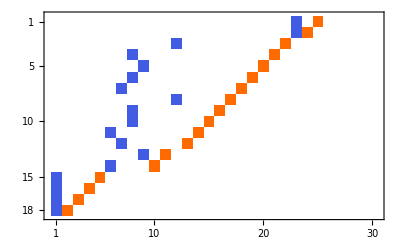

```mathematica
NullSpace[mat]//MatrixPlot
```

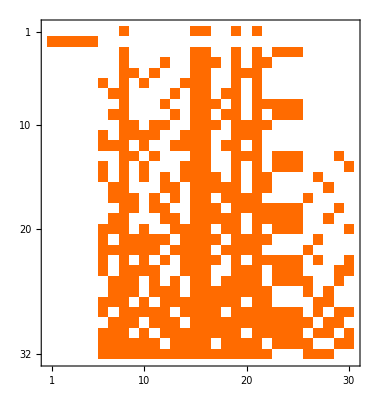

```mathematica
MatrixPlot[
Map[Last,Sort[Table[{SetsToLabel[{sets}],Length[Select[FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,sets}]]],SymbolLevel[#]==4&]],
ToAllVector[Select[FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,sets}]]],SymbolLevel[#]==4&]]},{sets,Subsets[Range[5]]}],#1[[2]]<#2[[2]]&]]
]
```

```mathematica
HowManyDifferentQuadrilaterals[form_]:=Block[{temp},
temp=Select[form,SymbolLevel[#]==4&];
temp=Map[WhichQuadrilateralPattern[SymbolToSets[#]]&,temp];
temp=DeleteDuplicates[temp];
Length[Select[temp,#≠-1&]]
]
```

```mathematica
TableForm[
Sort[
Table[
With[{formula=FindFullFormula[EdgeAdd[CycleGraph[5],Table[UndirectedEdge[6,k],{k,sets}]]]},
{SetsToLabel[{sets}],
Length[Select[formula,SymbolLevel[#]==4&]],
HowManyDifferentQuadrilaterals[formula],
Multicolumn[Select[Sort[Tally[Map[WhichQuadrilateralPattern[SymbolToSets[#]]&,Select[formula,SymbolLevel[#]==4&]]]],#[[1]]≠-1&]],Multicolumn[Select[Sort[Tally[Map[WhichTrianglePattern[SymbolToSets[#]]&,Select[formula,SymbolLevel[#]==4&]]]],#[[1]]≠-1&]],Framed[Multicolumn[Map[ColorShape,Select[formula,SymbolLevel[#]==4&]]]]}
]
,{sets,Subsets[Range[5]]}],#1[[2]]<#2[[2]]&
]
,
TableDepth->2,
TableHeadings->{None, {"connected to 6","count4", "count4quad","count4 quad", "count4 tria", "solutions 4"}}]
```

connected to 6 | count4 | count4quad | count4 quad | count4 tria | solutions 4
12345 | 5 | 0 |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
14♁2♁35♁6 | 13♁25♁4♁6 | 
 | 5 | 5 | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  |  | 1♁2♁35♁4 | 1♁24♁3♁5 | 13♁2♁4♁5
1♁25♁3♁4 | 14♁2♁3♁5 | 
2345 | 8 | 3 | {3,1} | {5,1}
{4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁24♁35♁6 | 16♁24♁3♁5 | 13♁25♁4♁6
16♁2♁35♁4 | 14♁2♁35♁6 | 13♁24♁5♁6
16♁25♁3♁4 | 14♁25♁3♁6 | 
1345 | 8 | 3 | {1,1} | {5,1}
{2,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
14♁2♁35♁6 | 13♁26♁4♁5 | 
1245 | 8 | 3 | {2,1} | {4,1}
{3,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁25♁36♁4 | 14♁2♁36♁5 | 13♁25♁4♁6
1♁24♁36♁5 | 14♁2♁35♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 14♁25♁3♁6 | 
1235 | 8 | 3 | {1,1} | {5,1}
{4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 13♁2♁46♁5 | 
1234 | 8 | 3 | {1,1} | {3,1}
{2,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁24♁3♁56 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
14♁2♁3♁56 | 13♁2♁4♁56 | 
345 | 11 | 5 | {1,1} | {3,1} | {5,2}
{2,1} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 16♁25♁3♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁24♁35♁6 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
16♁2♁35♁4 | 14♁2♁35♁6 | 13♁26♁4♁5 | 
234 | 11 | 5 | {1,1} | {3,2} | {5,1}
{2,1} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁24♁3♁56 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁35♁6 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
16♁2♁35♁4 | 14♁2♁3♁56 | 13♁2♁4♁56 | 
145 | 11 | 5 | {1,1} | {3,1} | {5,1}
{2,2} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 1♁24♁35♁6 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁25♁36♁4 | 14♁2♁36♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁36♁5 | 14♁2♁35♁6 | 13♁26♁4♁5 | 
125 | 11 | 5 | {1,1} | {3,1} | {5,1}
{2,1} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁24♁36♁5 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁25♁36♁4 | 14♁2♁36♁5 | 13♁2♁46♁5 | 
123 | 11 | 5 | {1,2} | {3,1} | {5,1}
{2,1} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 14♁2♁3♁56 | 13♁2♁4♁56 | 13♁24♁5♁6
1♁24♁3♁56 | 14♁2♁35♁6 | 13♁2♁46♁5 | 
245 | 12 | 5 | {1,1} | {3,2} | {5,1}
{2,1} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁36♁5 | 136♁2♁4♁5
1♁24♁36♁5 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁35♁6 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
235 | 12 | 5 | {1,1} | {3,1} | {5,2}
{2,1} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 16♁2♁35♁4 | 146♁2♁3♁5 | 13♁2♁46♁5
1♁25♁3♁46 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁35♁6 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
135 | 12 | 5 | {1,2} | {3,1} | {5,2}
{2,1} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁26♁35♁4 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 14♁2♁35♁6 | 13♁2♁46♁5 | 13♁24♁5♁6
134 | 12 | 5 | {1,2} | {3,1} | {5,1}
{2,2} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 1♁24♁35♁6 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁256♁3♁4 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁24♁3♁56 | 14♁2♁35♁6 | 13♁2♁4♁56 | 13♁24♁5♁6
124 | 12 | 5 | {1,1} | {3,2} | {5,1}
{2,2} | {4,1} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁36♁5 | 14♁2♁36♁5 | 13♁2♁4♁56
1♁25♁36♁4 | 1♁24♁35♁6 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁3♁56 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁24♁5♁6
45 | 15 | 5 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 16♁2♁35♁4 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁25♁36♁4 | 16♁25♁3♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁24♁36♁5 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 14♁2♁36♁5 | 136♁2♁4♁5 | 
34 | 15 | 5 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁26♁35♁4 | 16♁2♁35♁4 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁256♁3♁4 | 16♁25♁3♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁24♁3♁56 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 14♁2♁3♁56 | 13♁2♁4♁56 | 
23 | 15 | 5 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 16♁2♁35♁4 | 14♁2♁3♁56 | 13♁2♁46♁5
1♁25♁3♁46 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁3♁56 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁24♁35♁6 | 146♁2♁3♁5 | 13♁2♁4♁56 | 
15 | 15 | 5 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁26♁35♁4 | 1♁24♁36♁5 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁25♁3♁46 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁25♁36♁4 | 14♁2♁36♁5 | 13♁2♁46♁5 | 
12 | 15 | 5 | {1,2} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁3♁56 | 14♁2♁36♁5 | 13♁2♁46♁5
1♁2♁35♁46 | 1♁24♁36♁5 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁24♁5♁6
1♁25♁36♁4 | 14♁2♁3♁56 | 13♁2♁4♁56 | 
35 | 16 | 5 | {1,2} | {3,2} | {5,3}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁24♁35♁6 | 146♁2♁3♁5 | 13♁2♁46♁5
1♁26♁35♁4 | 16♁2♁35♁4 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁25♁3♁46 | 16♁25♁3♁4 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁246♁3♁5 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
25 | 16 | 5 | {1,2} | {3,2} | {5,2}
{2,2} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁24♁35♁6 | 146♁2♁3♁5 | 136♁2♁4♁5
1♁25♁3♁46 | 16♁2♁35♁4 | 14♁2♁36♁5 | 13♁2♁46♁5
1♁25♁36♁4 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁36♁5 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
24 | 16 | 5 | {1,2} | {3,3} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁35♁6 | 14♁2♁3♁56 | 136♁2♁4♁5
1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁36♁5 | 13♁2♁4♁56
1♁24♁3♁56 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁25♁4♁6
1♁24♁36♁5 | 16♁24♁3♁5 | 14♁25♁3♁6 | 13♁24♁5♁6
14 | 16 | 5 | {1,2} | {3,2} | {5,2}
{2,3} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁3♁56 | 14♁2♁36♁5 | 13♁2♁4♁56
1♁26♁35♁4 | 1♁24♁36♁5 | 14♁2♁35♁6 | 13♁26♁4♁5
1♁256♁3♁4 | 1♁24♁35♁6 | 14♁26♁3♁5 | 13♁25♁4♁6
1♁25♁36♁4 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁24♁5♁6
13 | 16 | 5 | {1,3} | {3,2} | {5,2}
{2,2} | {4,2} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁26♁35♁4 | 1♁24♁3♁56 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁256♁3♁4 | 1♁24♁35♁6 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 14♁2♁3♁56 | 13♁2♁4♁56 | 13♁24♁5♁6
5 | 20 | 5 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁26♁35♁4 | 1♁24♁36♁5 | 16♁24♁3♁5 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁25♁3♁46 | 1♁24♁35♁6 | 146♁2♁3♁5 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁36♁5 | 136♁2♁4♁5 | 13♁24♁5♁6
4 | 20 | 5 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁3♁56 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁2♁4♁56
1♁26♁35♁4 | 1♁24♁36♁5 | 16♁24♁3♁5 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁256♁3♁4 | 1♁24♁35♁6 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁36♁5 | 136♁2♁4♁5 | 13♁24♁5♁6
3 | 20 | 5 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁35♁46 | 1♁246♁3♁5 | 16♁25♁3♁4 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁26♁35♁4 | 1♁24♁3♁56 | 16♁24♁3♁5 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁256♁3♁4 | 1♁24♁35♁6 | 146♁2♁3♁5 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁3♁46 | 16♁2♁35♁4 | 14♁2♁3♁56 | 13♁2♁4♁56 | 13♁24♁5♁6
2 | 20 | 5 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁24♁3♁56 | 16♁25♁3♁4 | 14♁2♁36♁5 | 13♁2♁4♁56
1♁2♁35♁46 | 1♁24♁36♁5 | 16♁24♁3♁5 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁25♁3♁46 | 1♁24♁35♁6 | 146♁2♁3♁5 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁25♁36♁4 | 16♁2♁35♁4 | 14♁2♁3♁56 | 136♁2♁4♁5 | 13♁24♁5♁6
1 | 20 | 5 | {1,3} | {3,3} | {5,3}
{2,3} | {4,3} |  | {1,1} | {3,1} | {5,1}
{2,1} | {4,1} |  | 1♁2♁356♁4 | 1♁25♁3♁46 | 1♁24♁36♁5 | 14♁2♁35♁6 | 13♁2♁46♁5
1♁2♁35♁46 | 1♁25♁36♁4 | 1♁24♁35♁6 | 14♁26♁3♁5 | 13♁26♁4♁5
1♁26♁35♁4 | 1♁246♁3♁5 | 14♁2♁3♁56 | 14♁25♁3♁6 | 13♁25♁4♁6
1♁256♁3♁4 | 1♁24♁3♁56 | 14♁2♁36♁5 | 13♁2♁4♁56 | 13♁24♁5♁6